```mathematica
(*HNNP Ising AntiFerromagnetic model Renormalization group*)
```

```mathematica
(*-βH=-βJ0*(x0*x1+x1*x2+x2*x3+x3*x4)-βJ1(x1*x3)-βL0*(x0*x2+x2*x4)+βH(x0+x1+x2+x3+x4))
(*Comparing to Brunson2011, 
-βH=2I-K0*(x0*x1+x1*x2+x2*x3+x3*x4)-K1(x1*x3)-L0*(x0*x2+x2*x4)+B(x0+x1+x2+x3+x4))*)
(A[0]=4I=Log[C], A[1]=Exp[-4*K0]=κ,A[2]=Exp[-4*L0]=λ,μ=Exp[-2K1]=A[3])
```

```mathematica
dim=3;
A[3]=B[3]=μ;
Z0[x0_,x1_,x2_,x3_,x4_]:=Exp[-A[0]]*A[1]^(-(x0*x1+x1*x2+x2*x3+x3*x4)/4)*A[2]^(-(x0*x2+x2*x4)/4)*μ^(-(x0*x3+x1*x4)/2-y/2(x0*x4))
TrZ0[x0_,x2_,x4_]:=Sum[Sum[Z0[x0,x1,x2,x3,x4],{x1,-1,1,2}],{x3,-1,1,2}]
Z1[x0_,x2_,x4_]:=Exp[-B[0]/2]*B[1]^(-(x0*x2+x2*x4)/4)*B[2]^(-x0*x4/4)
```

```mathematica
i=0;
For[x0=-1,x0≤1,x0+=2,
For[x2=-1,x2≤1,x2+=2,
For[x4=-1,x4≤1,x4+=2,
leq[i]=Z1[x0,x2,x4];
req[i++]=TrZ0[x0,x2,x4];
]
]
]
```

```mathematica
Table[leq[i]==req[i],{i,0,7}]
```

{ⅇ^(-B[0]/2)/(√B[1] B[2]^(1/4))==(2 ⅇ^(-A[0]) μ^(-y/2))/(√A[2])+(ⅇ^(-A[0]) μ^(-1-y/2))/(A[1] √A[2])+(ⅇ^(-A[0]) μ^(1-y/2) A[1])/(√A[2]),ⅇ^(-B[0]/2) B[2]^(1/4)==(ⅇ^(-A[0]) μ^(1+y/2))/(√A[1])+(ⅇ^(-A[0]) μ^(y/2))/(√A[1])+ⅇ^(-A[0]) μ^(-1+y/2) √A[1]+ⅇ^(-A[0]) μ^(y/2) √A[1],(ⅇ^(-B[0]/2) √B[1])/B[2]^(1/4)==ⅇ^(-A[0]) μ^(-1-y/2) √A[2]+ⅇ^(-A[0]) μ^(1-y/2) √A[2]+2 ⅇ^(-A[0]) μ^(-y/2) √A[2],ⅇ^(-B[0]/2) B[2]^(1/4)==(ⅇ^(-A[0]) μ^(1+y/2))/(√A[1])+(ⅇ^(-A[0]) μ^(y/2))/(√A[1])+ⅇ^(-A[0]) μ^(-1+y/2) √A[1]+ⅇ^(-A[0]) μ^(y/2) √A[1],ⅇ^(-B[0]/2) B[2]^(1/4)==(ⅇ^(-A[0]) μ^(1+y/2))/(√A[1])+(ⅇ^(-A[0]) μ^(y/2))/(√A[1])+ⅇ^(-A[0]) μ^(-1+y/2) √A[1]+ⅇ^(-A[0]) μ^(y/2) √A[1],(ⅇ^(-B[0]/2) √B[1])/B[2]^(1/4)==ⅇ^(-A[0]) μ^(-1-y/2) √A[2]+ⅇ^(-A[0]) μ^(1-y/2) √A[2]+2 ⅇ^(-A[0]) μ^(-y/2) √A[2],ⅇ^(-B[0]/2) B[2]^(1/4)==(ⅇ^(-A[0]) μ^(1+y/2))/(√A[1])+(ⅇ^(-A[0]) μ^(y/2))/(√A[1])+ⅇ^(-A[0]) μ^(-1+y/2) √A[1]+ⅇ^(-A[0]) μ^(y/2) √A[1],ⅇ^(-B[0]/2)/(√B[1] B[2]^(1/4))==(2 ⅇ^(-A[0]) μ^(-y/2))/(√A[2])+(ⅇ^(-A[0]) μ^(-1-y/2))/(A[1] √A[2])+(ⅇ^(-A[0]) μ^(1-y/2) A[1])/(√A[2])}

```mathematica
SB[0]=Factor[Simplify[Solve[Factor[leq[0]*leq[1]*leq[2]*leq[3]]==Factor[req[0]*req[1]*req[2]*req[3]],B[0]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&C[1]==0]]
SB[1]=Factor[Simplify[Solve[Factor[leq[2]/leq[0]]==Factor[req[2]/req[0]],B[1]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&A[2]≥0&&C[1]==0]]
SB[2]=Factor[Simplify[Solve[Factor[leq[1]*leq[1]/leq[0]/leq[2]]==Factor[req[1]*req[1]/req[0]/req[2]],B[2]],A[0]∈Reals&&A[1]∈Reals&&A[2]∈Reals&&A[2]≥0&&C[1]==0]]
(*using Exp[-A[0]], C = Exp[A[0]]*)
```

{{B[0]→1/2 Log[(ⅇ^(4 A[0]) μ^4 A[1]^2)/((1+μ)^4 (μ+A[1]+μ^2 A[1]+μ A[1]^2)^2)]}}

{{B[1]→((1+μ)^2 A[1] A[2])/(1+μ A[1])^2}}

{{B[2]→(μ^(2 y) (μ+A[1])^2)/(1+μ A[1])^2}}

```mathematica
(*HN3 A[1] fixed point solution; only 2 fixed point A[1]=0 or 1 because μ≥1, A[1]≥0*)
Solve[κ==((1+μ)^2 κ)/(1+μ κ)^2*(μ^(2 y) (μ+κ)^2)/(1+μ κ)^2,κ]
```

{{κ→0},{κ→(-2 μ-μ^y-μ^(1+y)-μ^(y/2) (1+μ) √(4 μ-4 μ^2+μ^y))/(2 μ^2)},{κ→(-2 μ-μ^y-μ^(1+y)+μ^(y/2) (1+μ) √(4 μ-4 μ^2+μ^y))/(2 μ^2)},{κ→-(2 μ-μ^y-μ^(1+y)-μ^(y/2) (1+μ) √(-4 μ+4 μ^2+μ^y))/(2 μ^2)},{κ→-(2 μ-μ^y-μ^(1+y)+μ^(y/2) (1+μ) √(-4 μ+4 μ^2+μ^y))/(2 μ^2)}}

```mathematica
(* Another try with κ eliminated/simplified*)
Factor[(1+μ)^2/(1+μ κ)^2*(μ^(2 y) (μ+κ)^2)/(1+μ κ)^2]
Simplify[μ^(2 y) (1+μ)^2 (κ+μ)^2-(1+κ μ)^4]
(*Solve[1==(1+μ)^2/(1+μ κ)^2*(μ^(2 y) (μ+κ)^2)/(1+μ κ)^2,κ]*)
Solve[μ^(2 y) (1+μ)^2 (κ+μ)^2==(1+κ μ)^4,κ]
```

(μ^(2 y) (1+μ)^2 (κ+μ)^2)/(1+κ μ)^4

μ^(2 y) (1+μ)^2 (κ+μ)^2-(1+κ μ)^4

{{κ→(-2 μ-μ^y-μ^(1+y)-μ^(y/2) (1+μ) √(4 μ-4 μ^2+μ^y))/(2 μ^2)},{κ→(-2 μ-μ^y-μ^(1+y)+μ^(y/2) (1+μ) √(4 μ-4 μ^2+μ^y))/(2 μ^2)},{κ→-(2 μ-μ^y-μ^(1+y)-μ^(y/2) (1+μ) √(-4 μ+4 μ^2+μ^y))/(2 μ^2)},{κ→-(2 μ-μ^y-μ^(1+y)+μ^(y/2) (1+μ) √(-4 μ+4 μ^2+μ^y))/(2 μ^2)}}

```mathematica
fk1[μ_,y_]:=(-2 μ-μ^y-μ^(1+y)+μ^(y/2) (1+μ) √(4 μ-4 μ^2+μ^y))/(2 μ^2)
```

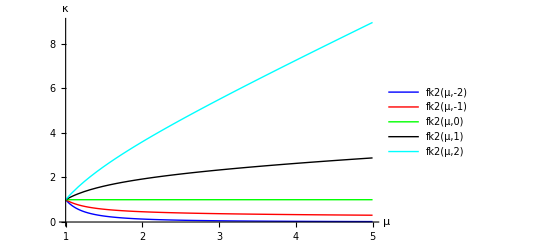

```mathematica
fk2[μ_,y_]:=(-2 μ+μ^y+μ^(1+y)+μ^(y/2) (1+μ) √(-4 μ+4 μ^2+μ^y))/(2 μ^2)
Plot[{fk2[μ,-2],fk2[μ,-1],fk2[μ,0],fk2[μ,1],fk2[μ,2]},{μ,1,5}, AxesLabel->{μ,κ},AxesOrigin->{1,0},PlotLegends->"Expressions", PlotStyle->{Blue,Red,Green,Black, Cyan}]
(**)
```

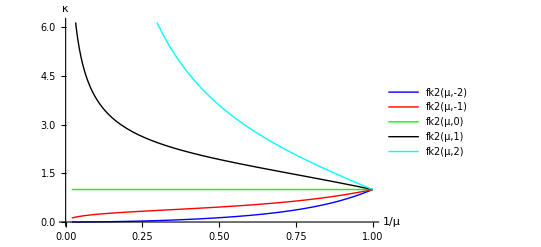

```mathematica
fk2[μ_,y_]:=(-2 /μ+μ^-y+μ^(-1-y)+μ^(-y/2) (1+1./μ) √(-4 /μ+4 /μ^2+μ^-y))/2*μ^2
Plot[{fk2[μ,-2],fk2[μ,-1],fk2[μ,0],fk2[μ,1],fk2[μ,2]},{μ,0.02,1}, AxesLabel->{1/μ,κ},AxesOrigin->{0,0},PlotLegends->"Expressions", PlotStyle->{Blue,Red,Green,Black, Cyan}]
(**)
```

```mathematica
fk2[0.00000001,-0.5]
```

0.00999999

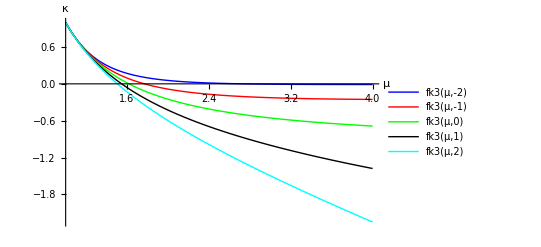

```mathematica
fk3[μ_,y_]:=(2 μ+μ^y+μ^(1+y)-μ^(y/2) (1+μ) √(-4 μ+4 μ^2+μ^y))/(2 μ^2)
Plot[{fk3[μ,-2],fk3[μ,-1],fk3[μ,0],fk3[μ,1],fk3[μ,2]},{μ,1,4}, AxesLabel->{μ,κ},AxesOrigin->{1,0},PlotLegends->"Expressions", PlotStyle->{Blue,Red,Green,Black, Cyan}]
(**)
```

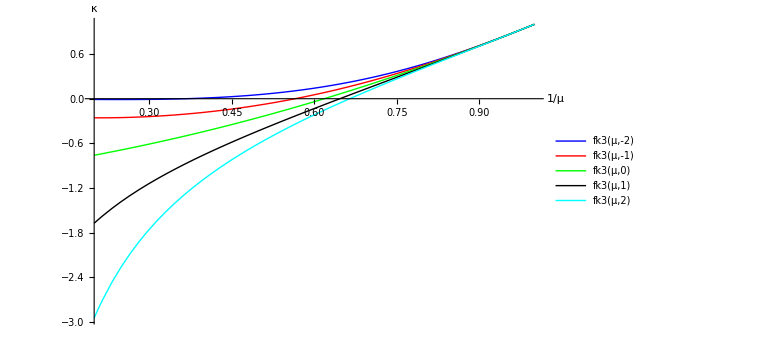

```mathematica
fk3[μ_,y_]:=(2 /μ+μ^-y+μ^(-1-y)-μ^(-y/2) (1+1./μ) √(-4 /μ+4 /μ^2+μ^-y))/2*μ^2
Plot[{fk3[μ,-2],fk3[μ,-1],fk3[μ,0],fk3[μ,1],fk3[μ,2]},{μ,0.2,1}, AxesLabel->{1/μ,κ},AxesOrigin->{0.2,0},PlotLegends->"Expressions", PlotStyle->{Blue,Red,Green,Black, Cyan}]
```

```mathematica
(*HN5 A[1] fixed point solution, A[1]≥1, μ≥1*)
y=1;
Factor[Solve[-(-1+μ+μ^2)/μ^2==0, μ ]]
Clear[y]
```

{{μ→1/2 (-1-√5)},{μ→1/2 (-1+√5)}}

```mathematica
Solve[1/2 (-μ+μ^2+√(-4+4 μ+5 μ^2-2 μ^3+μ^4))==0,μ]
```

{{μ→1/2 (-1+√5)}}

```mathematica
(*Eigenvalues*)
Clear[y]
K[κ_,λ_]:=((1+μ)^2 κ*λ)/(1+μ κ)^2
L[κ_,λ_]:=(μ^(2 y) (μ+κ)^2)/(1+μ κ)^2
{{Factor[D[K[κ,λ],κ]],Factor[D[K[κ,λ],λ]]},{Factor[D[L[κ,λ],κ]],Factor[D[L[κ,λ],λ]]}}
Simplify[Eigenvalues[{{Factor[D[K[κ,λ],κ]],Factor[D[K[κ,λ],λ]]},{Factor[D[L[κ,λ],κ]],Factor[D[L[κ,λ],λ]]}}]]
```

{{-(λ (1+μ)^2 (-1+κ μ))/(1+κ μ)^3,(κ (1+μ)^2)/(1+κ μ)^2},{-(2 (-1+μ) μ^(2 y) (1+μ) (κ+μ))/(1+κ μ)^3,0}}

{-((1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2+√(λ^2 (1+μ)^2 (-1+κ μ)^2-8 κ μ^(2 y) (-1+μ^2) (κ+μ+κ^2 μ+κ μ^2))))/(2 (1+κ μ)^3),-((1+μ) (-λ-λ μ+κ λ μ+κ λ μ^2-√(λ^2 (1+μ)^2 (-1+κ μ)^2-8 κ μ^(2 y) (-1+μ^2) (κ+μ+κ^2 μ+κ μ^2))))/(2 (1+κ μ)^3)}

```mathematica
Factor[D[L[κ,λ],κ]]
```

-(2 (-1+μ) μ^(2 y) (1+μ) (κ+μ))/(1+κ μ)^3

```mathematica
{{Factor[D[K[κ,λ],κ]],Factor[D[K[κ,λ],λ]]},{Factor[D[L[κ,λ],κ]],Factor[D[L[κ,λ],λ]]}}
```

{{-(λ (1+μ)^2 (-1+κ μ))/(1+κ μ)^3,(κ (1+μ)^2)/(1+κ μ)^2},{-(2 (-1+μ) μ^(2 y) (1+μ) (κ+μ))/(1+κ μ)^3,0}}

```mathematica
{{-(μ^(2*y+2) *(1+μ)^2 (-1))/(1)^3,0},{-(2 (-1+μ) μ^(2 y) (1+μ) (μ))/(1)^3,0}}
```

```mathematica
Eigenvalues[{{μ^(2+2 y) (1+μ)^2,0},{-2 (-1+μ) μ^(1+2 y) (1+μ),0}}]
```

{0,μ^(2+2 y) (1+μ)^2}

```mathematica
fm[μ_]:=μ^(2+2 y) (1+μ)^2
Solve[fm[μ]==1,μ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[μ^(2+2 y) (1+μ)^2==1,μ]